```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["PMdata.csv"];
dataNewton = Import["newtondata.csv"];
{x1,y1,z1,px1,py1,pz1,x2,y2,z2,px2,py2,pz2,x3,y3,z3,px3,py3,pz3,lx1,ly1,lz1,lx2,ly2,lz2,lx3,ly3,lz3,hamil}=data;
{x12,y12,z12,px12,py12,pz12,x22,y22,z22,px22,py22,pz22,x32,y32,z32,px32,py32,pz32,lx12,ly12,lz12,lx22,ly22,lz22,lx32,ly32,lz32,hamil2}=dataNewton;
```

/Users/zackarywindham/Research/Post-Minkowski/julia_code

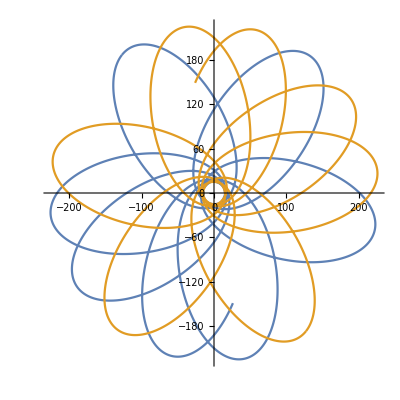

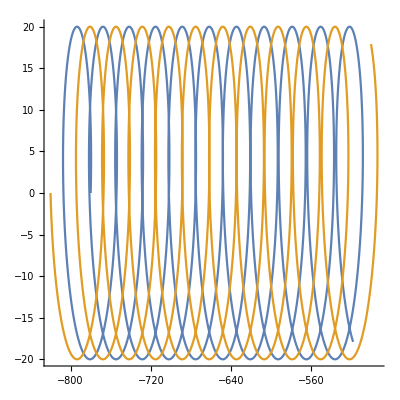

-Graphics-

```mathematica
ListPlot[{Transpose[{x1,y1}],Transpose[{x2,y2}](*,Transpose[{x3,y3}]*)},AspectRatio->1,Joined->True]
ListPlot[{Transpose[{x12,y12}],Transpose[{x22,y22}](*,Transpose[{x32,y32}]*)},AspectRatio->1,Joined->True]
ListPlot[Delete[hamil,1]]
```

```mathematica
Lx = lx1+lx2+lx3;
Ly= ly1+ly2+ly3;
Lz= lz1+lz2+lz3;
```